# Quantum Benchmarks

## HHL Matrix Creation

## Preliminaries

## Gates

```mathematica
Clear[Ctrl,Phase]
Ctrl[gate_]:=Ctrl[gate]=ArrayFlatten[{{Id,0},{0,gate}}]
Phase[ϕ_,pauli_]:=Phase[ϕ,pauli]=MatrixExp[ⅈ ϕ pauli]

{Id,X,Y,Z}=PauliMatrix/@{0,1,2,3};
H={{1,1},{1,-1}}/√2;
CNOT=Ctrl[X];
CZ=Ctrl[Z];
SWAP=ArrayFlatten[{{1,0,0},{0,X,0},{0,0,1}}];
NOTC=SWAP.CNOT.SWAP;
MyEcho[x_]:=Module[{},Print[x];x]
```

```mathematica
MatrixForm/@{Id,X,Y,Z,H,CNOT,CZ,SWAP,NOTC,Phase[Z,π/2],Phase[Y,π/16]}
```

{(1 | 0
0 | 1),(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1),(1/(√2) | 1/(√2)
1/(√2) | -1/(√2)),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0),(ⅈ | 0
0 | -ⅈ),(Cos[π/16] | Sin[π/16]
-Sin[π/16] | Cos[π/16])}

## Matrix Circuits

## VQE Ansatz for U

We seek an ansatz which is interleaved single-qubit and entangling layers; much like a VQE circuit. This is an arbitrary choice of course.

```mathematica
Clear[VQEAnsatz]
VQEAnsatz[width_Integer/;width≥3,depth_Integer/;depth≥1,singleQubitGateCount_Integer/;singleQubitGateCount≥1]:=Flatten@Table[{
SingleQubitLayer@@RandomChoice[Range@singleQubitGateCount,width],
EntanglingLayer@@If[EvenQ[width],
If[EvenQ[i],Table[2,{ii,1,width-1,2}],{1}~Join~Table[2,{ii,2,width-1,2}]~Join~{1}],
If[EvenQ[i],Table[2,{ii,1,width-1,2}]~Join~{1},{1}~Join~Table[2,{ii,2,width-1,2}]]
]
},
{i,1,depth}
]

Clear[UnitaryMatrixListQ,GateSetQ,RandomVQESample]
UnitaryMatrixListQ[list_]:=ListQ[list]∧(Length@list>0)∧And@@(UnitaryMatrixQ/@list)∧Equal@@(Dimensions/@list)∧(Dimensions@First@list=={2,2})
GateSetQ[assoc_]:=AssociationQ[assoc]∧UnitaryMatrixListQ@Values[assoc]
RandomVQESample[width_Integer/;width≥3,depth_Integer/;depth≥1,entanglingGate_?UnitaryMatrixQ,entanglingGateName_String,singleQubitGates_?GateSetQ,numeric_:True]:=
Module[{
singleQubitGatesN=Values@singleQubitGates//If[numeric,N,Identity],
entanglingGateN=entanglingGate//If[numeric,N,Identity],
ansatz,U,textual
},
ansatz=VQEAnsatz[3,3,Length@singleQubitGates];
U=Dot@@(ansatz//.{
SingleQubitLayer[l___,gateIdx_Integer,r___]:>SingleQubitLayer[l,singleQubitGatesN⟦gateIdx⟧,r],
EntanglingLayer[l___,gateIdx_Integer,r___]:>EntanglingLayer[l,If[gateIdx==1,Id,entanglingGateN],r]
}/.{
SingleQubitLayer->KroneckerProduct,
EntanglingLayer->KroneckerProduct
}
);
textual=ansatz//.{
SingleQubitLayer[gateIdcs__]:>MapIndexed[Function[{idx,lane},Keys[singleQubitGates]⟦idx⟧<>" "<>ToString[lane⟦1⟧]],{gateIdcs}],
EntanglingLayer[gateIdcs__]:>entanglingGateName<>" "<>StringRiffle[ToString/@{gateIdcs}]
}//Flatten;

<|
"ansatz"->ansatz,
"textual"->textual,
"U"->U//Chop
|>
]
```

The RandomVQESample function expects a circuit width (i.e. how many qubits U should act on), an ansatz depth, an entangling gate plus name, and a single qubit gate list defined in the following. This can of course be changed to include other rotations.

```mathematica
gateset=<|
"X"->X,
"Y"->Y,
"Z"->Z,
"H"->H,
"S"->Phase[Z,π/4],
"T"->Phase[Z,π/8],
"SX"->Phase[X,π/4],
"TX"->Phase[X,π/8],
"SY"->Phase[Y,π/4],
"TY"->Phase[Y,π/8]
|>;
MatrixForm/@%
```

<|X→(0 | 1
1 | 0),Y→(0 | -ⅈ
ⅈ | 0),Z→(1 | 0
0 | -1),H→(1/(√2) | 1/(√2)
1/(√2) | -1/(√2)),S→(ⅇ^((ⅈ π)/4) | 0
0 | ⅇ^(-(ⅈ π)/4)),T→(ⅇ^((ⅈ π)/8) | 0
0 | ⅇ^(-(ⅈ π)/8)),SX→(1/(√2) | ⅈ/(√2)
ⅈ/(√2) | 1/(√2)),TX→(1/2 (-1)^(1/8)-1/2 (-1)^(7/8) | 1/2 (-1)^(1/8)+1/2 (-1)^(7/8)
1/2 (-1)^(1/8)+1/2 (-1)^(7/8) | 1/2 (-1)^(1/8)-1/2 (-1)^(7/8)),SY→(1/(√2) | 1/(√2)
-1/(√2) | 1/(√2)),TY→(Cos[π/8] | Sin[π/8]
-Sin[π/8] | Cos[π/8])|>

```mathematica
RandomVQESample[3,3,CZ,"CZ",gateset]
```

<|ansatz→{SingleQubitLayer[9,3,9],EntanglingLayer[1,2],SingleQubitLayer[5,6,10],EntanglingLayer[2,1],SingleQubitLayer[2,5,8],EntanglingLayer[1,2]},textual→{SY 1,Z 2,SY 3,CZ 1 2,S 1,T 2,TY 3,CZ 2 1,Y 1,S 2,TX 3,CZ 1 2},U→{{-0.326641+0.135299 ⅈ,-0.326641+0.517982 ⅈ,0,0,0.135299+0.326641 ⅈ,0.517982+0.326641 ⅈ,0,0},{0.135299-0.597239 ⅈ,0.135299+0.326641 ⅈ,0,0,-0.597239-0.135299 ⅈ,0.326641-0.135299 ⅈ,0,0},{0,0,0.517982-0.326641 ⅈ,0.135299-0.326641 ⅈ,0,0,0.326641+0.517982 ⅈ,0.326641+0.135299 ⅈ},{0,0,-0.326641-0.135299 ⅈ,0.597239-0.135299 ⅈ,0,0,0.135299-0.326641 ⅈ,0.135299+0.597239 ⅈ},{-0.326641+0.135299 ⅈ,-0.326641+0.517982 ⅈ,0,0,-0.135299-0.326641 ⅈ,-0.517982-0.326641 ⅈ,0,0},{0.135299-0.597239 ⅈ,0.135299+0.326641 ⅈ,0,0,0.597239+0.135299 ⅈ,-0.326641+0.135299 ⅈ,0,0},{0,0,0.517982-0.326641 ⅈ,0.135299-0.326641 ⅈ,0,0,-0.326641-0.517982 ⅈ,-0.326641-0.135299 ⅈ},{0,0,-0.326641-0.135299 ⅈ,0.597239-0.135299 ⅈ,0,0,-0.135299+0.326641 ⅈ,-0.135299-0.597239 ⅈ}}|>

## Find Good Circuit Candidates

```mathematica
(* checks that the top bs x bs block has bs^2-minOffset many unique absolute value squared entries *)
Clear[CircuitCriterion]
CircuitCriterion[bs_Integer,threshold_:.01,minOffset_:1]:=Function[U,
(
Length@Union@Rationalize[#,threshold]&@Abs@N@Flatten@U⟦;;bs,;;bs⟧≥bs^2-minOffset
)∧(
(* condition number criterion *)
Min[SingularValueList[U⟦;;bs,;;bs⟧]]>.1
)
]
```

```mathematica
CircuitCriterion[5][RandomReal[{1,5},{10,10}]]&/@Range[10]
CircuitCriterion[5][IdentityMatrix[10]]
```

{True,False,False,False,False,False,False,True,False,False}

False

```mathematica
Clear[MatPlot]
MatPlot[U_?UnitaryMatrixQ,bs_Integer]:=BarChart3D[MyEcho[Abs[#]^2&/@U⟦;;bs,;;bs⟧],ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"FaceGrids"->None,"Canvas"->False]⟦1⟧//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&
```

Re-run the following or increase trials if it doesn’t print out a final matrix.

```mathematica
theVQE=Module[{
theVQE,
upperLeftBlockSize=4
},

Module[{
width=3,
depth=1,
entanglingGate=CZ,
entanglingGateName="CZ",
singleQubitGates=gateset,
i,maxTrials=10000,
criterionF=CircuitCriterion[upperLeftBlockSize,.025,5] (* play with the two threshold parameters in case you don't get a hit *)
},
For[i=1,i≤maxTrials,i++;
With[{
vqe=RandomVQESample[width,depth,entanglingGate,entanglingGateName,singleQubitGates,True]
},
If[criterionF@vqe["U"],
theVQE=vqe;
Break[];
]
]
]
];


MatPlot[theVQE["U"],upperLeftBlockSize]//Print;
theVQE
];

theVQE["textual"]
```

{{0.411152,0.0705425,0.015625,0.00268083},{0.0263483,0.153569,0.046875,0.273208},{0.015625,0.00268083,0.712928,0.122319},{0.046875,0.273208,0.078125,0.455346}}

-Graphics3D-

{TY 1,TY 2,Z 3,CZ 1 2,TX 1,Z 2,S 3,CZ 2 1,TY 1,TY 2,TY 3,CZ 1 2}

## Polynomial Coefficients

```mathematica
(*Finds the largest absolute value on the interval[-1,1]*)
findPolyMaxAbs[poly_]:=Module[{roots,optimaCandidates},roots=x/.NSolve[(D[poly,x]//Evaluate)==0,x];
optimaCandidates=Join[{-1},roots,{1}];
(poly/.x->optimaCandidates)//Abs//Max
];
(*Lowest degree problem specific polynomial*)
fitOddPoly[singularValues_]:=fitOptimizedPoly[singularValues,0,1];
(*Optimise the magnitude of the polynomial on[-1,1]*)
fitOptimizedPoly[singularValues_,numExtraPoints_,numRandomTrials_]:=Module[{distinctSVs=DeleteDuplicates[singularValues],fitPoints,tmpPoly,currentMinMax=Infinity,currentBestPoly},
For[j=0,j<numRandomTrials,j++,fitPoints=Join[distinctSVs,Table[RandomReal[{0,2}],{k,1,numExtraPoints}]];
fitPoints=DeleteCases[Join[fitPoints,-fitPoints]//N,0.0];
tmpPoly=InterpolatingPolynomial[{#,1/#}&/@fitPoints,x];
tmpPoly=((tmpPoly-(tmpPoly/.x->-x))/2)//Simplify;
currentBestPoly=If[findPolyMaxAbs[tmpPoly]<currentMinMax,tmpPoly,currentBestPoly];
currentMinMax=If[findPolyMaxAbs[tmpPoly]<currentMinMax,findPolyMaxAbs[tmpPoly],currentMinMax];];
currentBestPoly];
```

8.16340150682514398283728951355 x-93.535233688532741780363721773 x^3+301.218044752806861197313992307 x^5-363.174288416582953686884138733 x^7+147.48251920406232784444000572 x^9

{0.995078,0.936608,0.35037810813806799,0.0990974}

0.+112.125 x-1067.05 x^3+1909.86 x^5-954.93 x^7

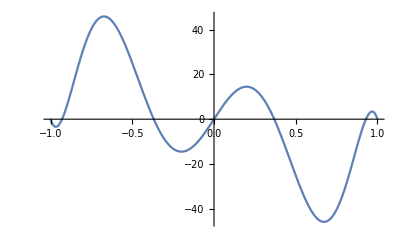

45.835

0.+114.151 x-1294.14 x^3+4070.97 x^5-4822.97 x^7+1934.02 x^9

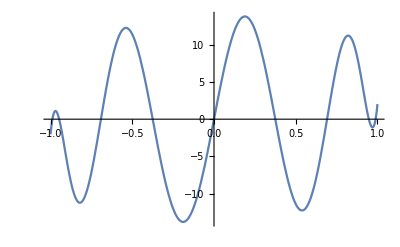

13.7782

```mathematica
(*Some tests and demos for the above*)
poly=8.1634015068251439828372895135544240474700927734375`30. x-93.53523368853274178036372177302837371826171875`30. x^3+301.21804475280686119731399230659008026123046875`30. x^5-363.1742884165829536868841387331485748291015625`30. x^7+147.482519204062327844440005719661712646484375`30. x^9
singularValues={0.99507773624,0.936608339348,0.350378108138067994,0.09909742093286229}
%//fitOddPoly
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs
optPoly1=fitOptimizedPoly[%%%%,1,100]
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs
(*fitOptimizedPoly[%%%%%%%,2,10000]
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs*)
```

```mathematica
(*Computes the pair of polynomials that correspond to the given real part, see more in https://arxiv.org/abs/1806.01838 *)
getPolyPairs[poly_,precision_]:=Module[{polyTry,K,roots,Qp,Zp,SRp,LRp,Ip,Wp,genRoots,zeroRoots,smallRealRoots,largeRealRoots,imgRoots,parityTrick,Bp,Cp},
polyTry=SetPrecision[poly,precision];
degree = (CoefficientList[polyTry,x]//Length)-1;
(K=Sqrt[-Coefficient[(1-polyTry^2//Expand),x^(2 degree)]])//Precision;
roots=x/.NSolve[(1-polyTry^2//Expand)==0,x,WorkingPrecision->precision];
(*p=ListPlot[{Re[#],Im[#]}&/@%,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]]];
Show[p,Graphics@Circle[{0,0},1]]*)
(genRoots=Select[roots,(Re[#]>0&& Im[#]>0)&]);
zeroRoots=(Select[roots,(#==0)&]);
smallRealRoots=(Select[roots,(#!=0&&Re[#]>-1&&Re[#]<1&& Im[#]==0)&]);
(smallRealRoots=Table[smallRealRoots[[4i-3]],{i,1,(smallRealRoots//Length)/4}]);
(largeRealRoots=Select[roots,(Re[#]≥1&& Im[#]==0)&]);
(imgRoots=Select[roots,(Re[#]==0&& Im[#]>0)&]);
Qp=(#[[2]]x^2-#[[1]]+I Sqrt[#[[2]]^2-1]x Sqrt[1-x^2])&/@({Abs[#]^2,Abs[#]^2+Sqrt[2(Re[#]^2+1)Im[#]^2+(Re[#]^2-1)^2+Im[#]^4]}&/@genRoots) ;
Zp=x^((zeroRoots//Length)/2);
SRp=(x^2-#^2)&/@smallRealRoots;
LRp=(Sqrt[#^2-1]x+I # Sqrt[1-x^2])&/@largeRealRoots;
Ip=(Sqrt[Abs[#]^2+1]x-I Abs[#]Sqrt[1-x^2])&/@imgRoots;
Wp=K*(Times@@Qp)*Zp*(Times@@SRp)*(Times@@LRp)*(Times@@Ip)//Expand//Simplify;
parityTrick=SetPrecision[Wp/.{Sqrt[1-x^2]->-I},precision];
Bp=SetPrecision[(parityTrick+(-1)^degree(parityTrick/.x->-x))/2//Simplify,parityTrick//Precision];
Cp=SetPrecision[(parityTrick-(-1)^degree(parityTrick/.x->-x))/2//Simplify,parityTrick//Precision];
{Bp,Cp}
]
```

True

8.1634 x-93.5352 x^3+301.218 x^5-363.174 x^7+147.483 x^9

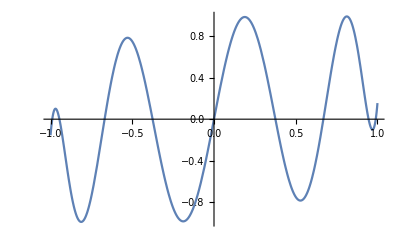

True

```mathematica
(*Some tests and demos for the above*)
{Bp,Cp}=getPolyPairs[ChebyshevT[5,x] ,110];
Bp^2+(1-x^2)Cp^2+ChebyshevT[5,x]^2//Expand//Chop;
(%//CoefficientList[#,x]&//Length)==1
poly=8.163401506825144 x-93.53523368853274 x^3+301.21804475280686 x^5-363.17428841658295 x^7+147.48251920406233 x^9
Plot[%,{x,-1,1}]
{Bp,Cp}=getPolyPairs[poly,30];
poly=SetPrecision[poly,30];
Bp^2+(1-x^2)Cp^2+poly^2//Expand//Chop;
(%//CoefficientList[#,x]&//Length)==1
```

```mathematica
(*Computes the sequence of angles for a given polynomial, see more in https://arxiv.org/abs/1806.01838 *)
getAngles[poly_,precision_]:=Module[{tmpPoly,agreement,tmpprecision,Bp,Cp,Mat,carved,phs,phaseGates,W,NewMat},
agreement=1;
tmpprecision=MachinePrecision;
phs={};
While[ ((agreement//Accuracy) <precision) ||(agreement>10^-precision),
tmpPoly=SetPrecision[poly,tmpprecision];
{Bp,Cp}=getPolyPairs[tmpPoly,tmpprecision];
(Mat={{tmpPoly+ I Bp,  Sqrt[1-x^2] Cp},{- Sqrt[1-x^2] Cp,tmpPoly-I Bp}})//MatrixForm;
carved=NestList[carveLastAngle[#[[1]]]&,{Mat,{}},(tmpPoly//CoefficientList[#,x]&//Length)-1];
phs=Join[{(carved//Last)[[1]][[1]][[1]]},(#[[2]]&/@ carved)//Reverse//Most];
NewMat=getWMatrix[phs];
agreement=(NewMat[[1,1]]-tmpPoly-I Bp)//Expand//CoefficientList[#,x]&//Abs//Total;
Print[tmpprecision];
tmpprecision=2tmpprecision];
phs//Arg
];
carveLastAngle[Mat_]:=Module[{phase,outMat},
phase=(Coefficient[Mat[[1,1]],x,Exponent[Mat[[1,1]],x]]/(Coefficient[Mat[[1,2]]/.{Sqrt[1-x^2]->-I},x,(Exponent[Mat[[1,1]],x]-1)]))//Sqrt;
outMat=Mat.{{Conjugate[phase],0},{0,phase}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand;
outMat=outMat/.x^b_/;b≥Exponent[Mat[[1,1]],x]+1->0;
outMat=outMat/.Sqrt[1-x^2]x^b_/;b≥Exponent[Mat[[1,1]],x]->0;
{outMat, phase}
];
getWMatrix[phs_]:=Module[{phaseGates,W},
phaseGates=Table[{{phs[[i]],0},{0,Conjugate[phs[[i]]]}},{i,1,Length[phs]}];
(W={{x,I Sqrt[1-x^2]},{I Sqrt[1-x^2],x}})//MatrixForm;
(Dot@@((phaseGates//Most).W)).(phaseGates//Last)//Expand
];
WAnglesToRAngles[phs_]:=Module[{tmpPhs},tmpPhs=phs;tmpPhs[[1]]+=Last[phs]+((Mod[(Length[phs]),4])-1)Pi/2;Drop[tmpPhs,-1]-Pi/2]
getRMatrix[angles_]:=Module[{phaseGates,R},
phaseGates=Table[{{Exp[I angles[[i]]],0},{0,Exp[-I angles[[i]]]}},{i,1,Length[angles]}];
(R={{x, Sqrt[1-x^2]},{ Sqrt[1-x^2],-x}})//MatrixForm;
(Dot@@(phaseGates.R))//Expand
];
```

```mathematica
(*Some tests and demos for the above*)
angles=getAngles[ChebyshevT[10,x],20]//Chop
(getWMatrix[Exp[I%]])[[1,1]]-ChebyshevT[10,x]//Chop
(getRMatrix[%%//WAnglesToRAngles])[[1,1]]-ChebyshevT[10,x]//Expand//Chop
tmpPoly=poly/findPolyMaxAbs[poly]//Expand
angles=getAngles[%,20]
((getWMatrix[Exp[I%]//Reverse])[[1,1]]-%%)//CoefficientList[#,x]&//Re//Abs//Total//Chop
((getRMatrix[%%//WAnglesToRAngles])[[1,1]]-%%%)//CoefficientList[#,x]&//Re//Abs//Total//Chop
(*This is what we need to feed to the QSVT circuit*)
%%%//WAnglesToRAngles//Reverse//SetPrecision[#,MachinePrecision]&
```

MachinePrecision

2 MachinePrecision

4 MachinePrecision

{-0.785398163397448309615660845819875721049292349843776,0,0,0,0,0,0,0,0,0,0.785398163397448309615660845819875721049292349843776455243736148}

0

0

8.27720505405564551123137 x-94.8391805023565269774823 x^3+305.417235733924878686473 x^5-368.237192923995131082338 x^7+149.538529045778466957024 x^9

MachinePrecision

2 MachinePrecision

4 MachinePrecision

{-0.4089016354718945718135334967006983099950756164053047,0.3584552943894671048484011800076354034164197980374832,0.1360371483773155434284907327899614637077372110351559,0.0886809496145304613460840510429002668549891971876787176,-0.2528935548135681433296103510403283372731718347291814506,-0.252893554813568143329610349898074055085989847324254902989,0.08868094961453046134608405330722434520542878323323955647261,0.1360371483773155434284907341105314741910666874760349903966,0.3584552943894671048484011799913513068867227374364910563946569,1.16189469132300204741778819472426882125374014488101127316880148}

0

0

{-1.21234,-1.43476,-1.48212,-1.82369,-1.82369,-1.48212,-1.43476,-1.21234,0.752993}

```mathematica
Clear[anglesForCircuit];
anglesForCircuit[vqe_Association,verbose_Boolean:False]:=Module[{
U=vqe["U"],
blockEncoding,
SVs,
interPolys, interPolysMaxAbs,
objectiveFunction, optimumDeg,
interPoly,
print=If[verbose,Print,Identity]
},
blockEncoding=U[[1;;Length[U]/2,1;;Length[U]/2]];
blockEncoding//MatrixForm//print;
MatPlot[U,Length[blockEncoding]]//print;
blockEncoding//Inverse//MatrixForm//print;
MatInvPlot[blockEncoding]//print;
blockEncoding.Inverse[blockEncoding]//MatrixForm//Chop//print;
SVs=SingularValueList[blockEncoding];
SVs=DeleteDuplicatesBy[SVs,Round[500*#]&];
print[SVs];
print[DeleteDuplicates[SVs]];
interPolys=Table[fitOptimizedPoly[SVs,i,100^i],{i,0,1}];
interPolysMaxAbs=findPolyMaxAbs/@interPolys;
For[i=1,i≤Length[interPolys],i++,Plot[interPolys[[i]],{ x,-1,1}]//print];
objectiveFunction=1/interPolysMaxAbs/(Length[CoefficientList[#,x]]&/@interPolys);
optimumDeg=(Position[objectiveFunction,Max[objectiveFunction]]//Flatten)[[1]];
print[optimumDeg];
interPoly=interPolys[[optimumDeg]];
interPoly=0.9999*interPoly/findPolyMaxAbs[interPoly]//Expand;
print[interPoly];
getAngles[interPoly,20]//WAnglesToRAngles//Reverse//SetPrecision[#,MachinePrecision]&
];
Clear[MatInvPlot];
MatInvPlot[mat_]:=BarChart3D[MyEcho[Abs[#]^2&/@Inverse[mat]],ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"FaceGrids"->None,"Canvas"->False]⟦1⟧//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&;
```

```mathematica
anglesForCircuit[theVQE]
```

{{0.411152,0.0705425,0.015625,0.00268083},{0.0263483,0.153569,0.046875,0.273208},{0.015625,0.00268083,0.712928,0.122319},{0.046875,0.273208,0.078125,0.455346}}

{{1.80248,0.197521,0.0395043,0.118513},{0.309256,1.15124,0.00677786,0.690744},{0.0395043,0.118513,1.0395,0.0666157},{0.00677786,0.690744,0.178351,0.388265}}

MachinePrecision

2 MachinePrecision

{-2.29647,-2.29647,-7.02536}

## Export Candidates to Python

```mathematica
exportCandidate[vqe_Association]:=Module[{str=""},
str=str<>"{\n    \"circuit\": [";
str=str<>StringRiffle["("<>StringReplace["\""<>StringReplace[#," "->"\" ",1]," "->", "]<>")"&/@vqe["textual"],", "]<>"],\n";
str=str<>"    \"angles\": [";
str=str<>StringRiffle[ToString/@anglesForCircuit[vqe],", "]<>"],\n";
str=str<>"    \"unitary real\": [";
str=str<>StringRiffle[("["<>StringRiffle[ToString/@#,", "]<>"]")&/@Re[vqe["U"]],", "]<>"],\n";
str=str<>"    \"unitary imag\": [";
str=str<>StringRiffle[("["<>StringRiffle[ToString/@#,", "]<>"]")&/@Im[vqe["U"]],", "]<>"],\n";
str=str<>"}";
str
]
```

```mathematica
exportCandidate[theVQE]
```

{{0.411152,0.0705425,0.015625,0.00268083},{0.0263483,0.153569,0.046875,0.273208},{0.015625,0.00268083,0.712928,0.122319},{0.046875,0.273208,0.078125,0.455346}}

{{1.80248,0.197521,0.0395043,0.118513},{0.309256,1.15124,0.00677786,0.690744},{0.0395043,0.118513,1.0395,0.0666157},{0.00677786,0.690744,0.178351,0.388265}}

MachinePrecision

2 MachinePrecision

{
    "circuit": [("TY", 1), ("TY", 2), ("Z", 3), ("CZ", 1, 2), ("TX", 1), ("Z", 2), ("S", 3), ("CZ", 2, 1), ("TY", 1), ("TY", 2), ("TY", 3), ("CZ", 1, 2)],
    "angles": [-2.29647, -2.29647, -7.02536],
    "unitary real": [[0.426777, 0.176777, 0., 0., 0.176777, 0.0732233, 0., 0.], [0.103553, -0.25, 0.176777, 0.426777, 0.25, -0.603553, 0.0732233, 0.176777], [0., 0., -0.426777, 0.176777, 0., 0., -0.176777, 0.0732233], [-0.176777, 0.426777, 0.25, 0.603553, -0.0732233, 0.176777, -0.103553, -0.25], [-0.603553, -0.25, -0.176777, 0.0732233, 0.25, 0.103553, 0.426777, -0.176777], [-0.0732233, 0.176777, 0., 0., 0.176777, -0.426777, 0., 0.], [0.176777, 0.0732233, 0.25, -0.103553, -0.426777, -0.176777, 0.603553, -0.25], [0., 0., 0.0732233, 0.176777, 0., 0., -0.176777, -0.426777]],
    "unitary imag": [[0.478553, 0.198223, -0.125, 0.0517767, 0.551777, 0.228553, 0.301777, -0.125], [-0.125, 0.301777, -0.125, -0.301777, -0.0517767, 0.125, -0.0517767, -0.125], [0.125, 0.0517767, -0.728553, 0.301777, -0.301777, -0.125, 0.0517767, -0.0214466], [0.125, -0.301777, -0.125, -0.301777, 0.0517767, -0.125, -0.0517767, -0.125], [-0.125, -0.0517767, -0.125, 0.0517767, 0.301777, 0.125, 0.301777, -0.125], [0.228553, -0.551777, 0.125, 0.301777, -0.198223, 0.478553, 0.0517767, 0.125], [0.125, 0.0517767, -0.125, 0.0517767, -0.301777, -0.125, 0.301777, -0.125], [-0.125, 0.301777, 0.0214466, 0.0517767, -0.0517767, 0.125, 0.301777, 0.728553]],
}

This can be copied as-is as valid JSON to python, by right-clicking and selecting “copy as... plain text”